```mathematica
rhs[ka_,z_]:=-Sqrt[z^2-ka^2]
```

```mathematica
lhs[ka_]:=ka Cot[ka]
```

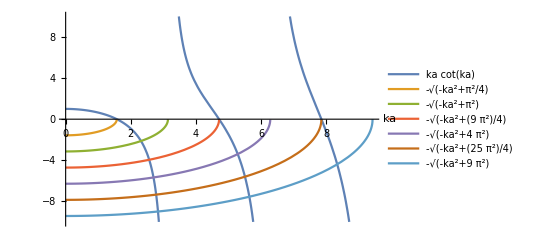

```mathematica
Plot[{ka Cot[ka],Evaluate@Table[rhs[ka,z],{z,Pi/2,3Pi,Pi/2}]},{ka,0,3Pi},PlotRange->{-10,10},AxesLabel->{ka,""},PlotLegends->"Expressions"]
```